## Initialization

```mathematica
$FKKSRoot = NotebookDirectory[]<>"../";
$SolutionPath = $FKKSRoot<>"Solutions/";
PlotPath = $FKKSRoot<>"Plots/";
LogFile = $FKKSRoot<>"Logs/LogFile.log";
PlotFileExtension = ".png";
NumberofSlaveKernels = Automatic; (*Default should be Automatic*)

(*Import some helper functions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "HelperFunctions.wl"}]]

(*Setup xAct definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "xActSetup.wl"}]]

(*Setup Proca Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "KerrWithProca.wl"}]]

(*Import mode overtone worker function for iteration routine*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "ModeOvertoneWorker.wl"}]]

(*Setup Energy Momentum Definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "EnergyMomentum.wl"}]]

(*Setup MST Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "MSTSolver.wl"}]]

(*Setup Inhomogeneous Teukolsky Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "TeukolskySolver.wl"}]]
```

## Setup

```mathematica
$FKKSRoot = NotebookDirectory[]<>"../";
$Messenger = "$Messenger is a global variable that tracks various computation steps. OwnValue can be tracked with Monitor[expr, $Messenger] or Dynamic[$Messenger]";
SolutionPath = $FKKSRoot<>"Solutions/";
Get[FileNameJoin[{NotebookDirectory[], "../Packages", "xActSetup.wl"}]]
Get[FileNameJoin[{NotebookDirectory[], "../Packages","EnergyMomentum.wl"}]]
Get["KerrWithProca`"]
Get["SpinWeightedSpheroidalHarmonics`"]
Get["Teukolsky`"]
```

```mathematica
θϵ=10^-5;

Teukrho = 1/(r[]-I*a*Cos[θ[]]);
Teukrhob = 1/(r[]+I*a*Cos[θ[]]);
KerrΔ = r[]^2-2*M*r[]+a^2;
KerrΣ = r[]^2+a^2*Cos[θ]^2;

L[s_][expr_]:=
Block[{tmp},
With[{EXPRESSION = FromxActVariables[expr]},
tmp = (D[#,θ]- I/Sin[θ] D[#,ϕ]-I*a*Sin[θ]D[#,t]+s*Cot[θ]*#)&@EXPRESSION
];
ToxActVariables[tmp]
]

Jp[expr_]:=
Block[{tmp},
With[{EXPRESSION = FromxActVariables[expr], Δ = FromxActVariables[KerrΔ]},
tmp=(D[#,r]-1/Δ((r^2+a^2)D[#,t]+a*D[#,ϕ]))&@EXPRESSION
];
ToxActVariables[tmp]]
```

## Source Definition

```mathematica
tmpsol = getResults[$SolutionPath, {{"m",1},{"n",0}, {"μNv", "1_5"}}]//First;
flutmp = tmpsol["Derived", "Einf"];
entmp = tmpsol["Derived", "Normalization", "TotalEnergy"];
rattmp = flutmp/entmp^2
```

7.87657×10^-6

```mathematica
Dynamic[$Messenger]
```

```mathematica
TnnExpl = Tnn[tmpsol, AsOptimized->True];
TmnExpl = Tmbn[tmpsol, AsOptimized->True];
TmmExpl = Tmbmb[tmpsol, AsOptimized->True];
```

```mathematica
TmnExpl[0,2,1,0]
```

2.72828×10^-6+0.000252667 ⅈ

#### Nils Code

```mathematica
prec=SetPrecision[#,20]&;
para=prec@{χ->0.9,μ->1/5,mT->2,ωT->(2*tmpsol["Solution", "ω"]//Re)};

rstart1 = 1.436;
rstop1=868;
θstart1=10^-4;
θstop1 = π-10^-4;

rstart=prec@rstart1;
rstop=prec@rstop1;
θstart=prec@θstart1;
θstop=prec@θstop1;
rmesh=99;
thmesh=49; (*This HAS to be an odd number to hit the last θstop exactly*)
rdatapoint[x_]:=(rstop-rstart)/((rmesh+1)^4-1) x^4+rstart-(rstop-rstart)/((rmesh+1)^4-1);
rrange=prec@rdatapoint[Range[1,rmesh+1]];
θrange=prec@Range[θstart,θstop,(θstop-θstart)/thmesh];


mTeu = 2;
```

```mathematica
tnntemp=Monitor[
Parallelize@Table[
(-1)^mTeu 1/(2*π) FourierCoefficient[
FourierTransform[
TnnExpl[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,
t,ωT]/.{DiracDelta[a_]:>1},
ϕ,mTeu, FourierParameters->{1,1}],
{j,1,Length[rrange]},{k,1,Length[θrange]}],
{j,k}];
```

PrintAsCharacter::argx: PrintAsCharacter called with 0 arguments; 1 argument is expected.

```mathematica
tnntempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tnntemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TnnInterNumRe[rr_,θθ_]:=Interpolation[tnntempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tnntempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tnntemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TnnInterNumIm[rr_,θθ_]:=Interpolation[tnntempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TnnInter[rr_,θθ_]:=TnnInterNumRe[r,θ]+I TnnInterNumIm[r,θ]/.{r->rr,θ->θθ};
```

```mathematica
TnnInter[1.7,π/2]/(2*π)
TnnExpl[0,1.7,π/2,0]
(*Plot[{TnnInter[r,π/2],TnnExpl[0,r,π/2,0]}//Re, {r,1.5,5}]*)
```

-0.0000418335+0.0000524535 ⅈ

0.0000201545

```mathematica
FourierTransform[1 ,t,wt]
FourierTransform[Cos[tt wt], tt,wt]
```

√(2 π) DiracDelta[wt]

FourierTransform[Cos[tt wt],tt,wt]

```mathematica
Print["---------------------------------------------------------------------"];
Print["Generating: Tnn..."];
tnntemp=Monitor[Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TnnExpl[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}],{j,k}];
tnntempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tnntemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TnnInterNumRe[rr_,θθ_]:=Interpolation[tnntempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tnntempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tnntemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TnnInterNumIm[rr_,θθ_]:=Interpolation[tnntempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TnnInter[rr_,θθ_]:=TnnInterNumRe[r,θ]+I TnnInterNumIm[r,θ]/.{r->rr,θ->θθ};

Print["Generating: Tmn..."];
tmntemp=Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TmnExpl[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}];
tmntempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmntemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmnInterNumRe[rr_,θθ_]:=Interpolation[tmntempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tmntempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmntemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmnInterNumIm[rr_,θθ_]:=Interpolation[tmntempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TmnInter[rr_,θθ_]:=TmnInterNumRe[r,θ]+I TmnInterNumIm[r,θ]/.{r->rr,θ->θθ};

Print["Generating: Tmm..."];
tmmtemp=Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TmmExpl[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}];
tmmtempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmmtemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmmInterNumRe[rr_,θθ_]:=Interpolation[tmmtempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tmmtempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmmtemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmmInterNumIm[rr_,θθ_]:=Interpolation[tmmtempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TmmInter[rr_,θθ_]:=TmmInterNumRe[r,θ]+I TmmInterNumIm[r,θ]/.{r->rr,θ->θθ};
Print["Generating: Done."];
Print["---------------------------------------------------------------------"];

(*Computing integrand of Tlmω*)
TijtoExpl=Table[{ToExpression["PrivateTeukolsky`T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ]},{j,{"nn","mn","mm"}}]//Flatten;
dTijtoExpl=Table[{ToExpression["PrivateTeukolsky`d"<>ToString[i]<>ToString["T"]<>ToString[j]]->D[ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ],{r,θ}[[i]]]},{i,{1,2}},{j,{"nn","mn","mm"}}]//Flatten;
ddTijtoExpl=Table[{ToExpression["PrivateTeukolsky`d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->D[D[ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ],{r,θ}[[k]]],{r,θ}[[i]]]},{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}]//Flatten;
TTtemp=(TeukolskyTintegrand/.{χ->spin,μ->Procamass,ωT->ωTeu,mT->mTeu}//.ddTijtoExpl//.dTijtoExpl//.TijtoExpl);
TeukolskyTintegrandExpl[rr_,θθ_]:=TTtemp/.{r->rr,θ->θθ};
```

## _

```mathematica
testsol = getResults[SolutionPath, {{"m",1},{"n",0}, {"μNv","11_25"}}][[3]];
testsol["Solution", "R"]=testsol[["Solution", "R(r)"]];
r1start =  testsol[["Solution", "R"]]["Domain"]//First//First;
r1dom = testsol[["Solution", "R"]]["Domain"]//First//Last;
rdom = testsol["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#, testsol["Parameters", "χ"]]&;

testsol[["Solution","ω"]] = testsol[["Solution","ω"]] //Re;
testsol[["Solution", "S"]]={θ}|->Evaluate[Sum[C[tempiter]*SphericalHarmonicY[Abs[testsol["Parameters", "m"]]+2*tempiter+testsol["Parameters", "η"],testsol["Parameters", "m"],θ,ϕ]*Exp[-I*testsol["Parameters", "m"]*ϕ], {tempiter,0,testsol["Parameters", "KMax"]}]/.testsol["Solution", "AngularKernelVector"]];
ωvalue = testsol["Solution", "ω"];
νvalue = testsol["Solution", "ν"];
χvalue = testsol["Parameters", "χ"];
teukL = 2;
teukM = 2;
```

```mathematica
ωvalue
```

0.378573929310266762

```mathematica
TeukSource = TeukolskySource[testsol];
```

```mathematica
Tlmw = TeukolskySourceModal[testsol,2,2];
```

```mathematica
dat=Flatten[Table[{{l,m},TeukolskyZInfinity[testsol, Tlmw, l,m]//Abs}, {l,2,6},{m,-l,l}],1]
```

{{{2,-2},0.000187048},{{2,-1},0.000148735},{{2,0},0.000120498},{{2,1},0.0000712939},{{2,2},0.00174782},{{3,-3},0.000189834},{{3,-2},0.0000287683},{{3,-1},0.000267785},{{3,0},0.000817495},{{3,1},0.000723824},{{3,2},0.0150506},{{3,3},0.00296043},{{4,-4},0.00045773},{{4,-3},0.000699895},{{4,-2},0.00019043},{{4,-1},0.00180573},{{4,0},0.00194439},{{4,1},0.00203274},{{4,2},0.0250589},{{4,3},0.00233923},{{4,4},0.00253031},{{5,-5},0.00116238},{{5,-4},0.00122693},{{5,-3},0.00123778},{{5,-2},0.000418756},{{5,-1},0.00127187},{{5,0},0.00130472},{{5,1},0.00134801},{{5,2},0.0346748},{{5,3},0.0014548},{{5,4},0.00151828},{{5,5},0.00158856},{{6,-6},0.000771908},{{6,-5},0.000772376},{{6,-4},0.00077739},{{6,-3},0.000786099},{{6,-2},0.000339371},{{6,-1},0.000811878},{{6,0},0.000828345},{{6,1},0.000846974},{{6,2},0.0360261},{{6,3},0.00089045},{{6,4},0.000915319},{{6,5},0.00094233},{{6,6},0.00097155}}

```mathematica
TeukolskyZInfinity[testsol, Tlmw, 5,1]
```

0.000576674+0.00121843 ⅈ

```mathematica
EnergyFlux[testsol, TeukolskyTlmw->Tlmw]
```

0.0000424072

0.00409369+0.000258035 ⅈ

```mathematica
precision = 40;
teukRadMST = TeukolskyRadial[-2,teukL, teukM, SetPrecision[χvalue,precision],  SetPrecision[ωvalue,precision], Method->"MST"];
Plot[teukRadMST["In"][r]//Abs, {r,Sequence@@rdom}, PlotLabel->"Method -> MST", WorkingPrecision->precision]
teukRad["In"]["Amplitudes"]
```

```mathematica
teukRadNumInt = TeukolskyRadial[-2,teukL, teukM, χvalue, ωvalue, Method->{"NumericalIntegration", "Domain"->{"In"->rdom, "Up"-> rdom}}];
Plot[teukRadNumInt["In"][r]//Abs, {r,Sequence@@rdom}, PlotLabel->"Method -> NumericalIntegration"]
teukRadNumInt["In"]["Amplitudes"]
```

```mathematica
teukRadHeunC = TeukolskyRadial[-2,teukL, teukM, χvalue, ωvalue, Method->"HeunC"];
Plot[teukRadHeunC["In"][r]//Abs, {r,Sequence@@rdom}, PlotLabel->"Method -> HeunC"]
teukRadHeunC["In"]["Amplitudes"]
```

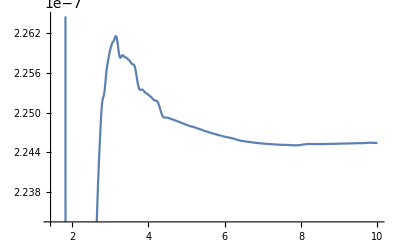

```mathematica
Plot[(teukRadNumInt["In"][r] - teukRadMST["In"][r])/(teukRadNumInt["In"][r])//Abs, {r,1.44,10}]
```

```mathematica
precision = 18;
teukRadMST = TeukolskyRadial[-2,teukL, teukM, SetPrecision[χvalue,precision],  SetPrecision[ωvalue,precision], Method->"MST"];
teukRad["In"]["Amplitudes"]["Incidence"]
```

55.03444774122415559880395+74.18364092556108168908255 ⅈ